```mathematica
FourierTransform
```

```mathematica
FourierSequenceTransform
```

```mathematica
DiscreteConvolve
```

```mathematica
ListConvolve
```

```mathematica
data=Import["D:\\data.csv",CharacterEncoding->"UTF-8"];
data=data[[2;;-1]];
```

```mathematica
data//Length
```

11687

```mathematica
characters=Union[Flatten[Characters[#]&/@data]];
```

```mathematica
ClearAll[cPosition];
cPosition[c_]:=0
(cPosition[characters[[#]]]=#)&/@Range[Length[characters]];
```

```mathematica
ToSequence[x_]:=Module[{c=Characters[x]},
(cPosition[#])&/@c[[1]]
]
```

```mathematica
SparseArray[{{1,1}->1,{2,2}->2,{3,3}->3,{1,3}->4}]
```

```mathematica
newdata=SparseArray[Flatten[(ind=#;({ind,#}->1)&/@ToSequence[data[[ind]]])&/@Range[Length[data]]]];
```

```mathematica
newdata[[1]]
```

SparseArray[<58>, {1917}]

```mathematica
dwd=DiscreteWaveletTransform[Total[newdata],DaubechiesWavelet[]];
thr=WaveletThreshold[dwd];
InverseWaveletTransform[thr]
```

{33.113,32.2853,41.5521,48.1141,51.9713,56.5532,43.6429,35.4197,7.34782,2110.41,2005.48,8.20507,59.7144,17.9424,31.7925,30.7387,8.83871,1013.67,-11.7479,134.723,1.2504,-57.2113,18.703,933.846,48.7816,55.2561,21.7298,-1.07833,54.0284,5305.46,-2.03386,87.1129,19.877,-5.45623,10.6078,15.5795,9.45878,6.31026,13.3667,17.6888,19.2764,21.5968,26.5534,30.8037,34.3475,38.0807,2.47242,-22.5943,-2.13395,6.12748,11.6687,577.709,6.59006,6.24565,4.09671,3126.77,102.719,1.59355,23.166,11.8617,27.1822,35.3686,582.379,5.39454,1976.41,3.4277,-2.32548,1.19935,39.0607,67.7215,8666.42,1859.43,5.85373,9.36134,12.6186,15.9429,6.78951,0.979514,4.38437,5.32012,3.78676,2.91499,6.18055,8.33752,9.38589,10.7313,-6.33479,-18.4675,-19.9782,568.737,62.1186,104.422,41.3384,6.49321,16.1348,13.8561,-0.342682,-11.3475,2.34292,9.41627,9.87255,12.1019,6.72315,3.383,3050.79,2.80715,240.886,9.2868,33.832,-10.2564,1986.98,-3.792,-5.72492,-5.6136,953.852,29.1317,48.2325,69.2376,70.1955,76.525,28.7931,-4.453,11.0957,13.5699,2.96957,-4.12747,38.1231,67.1509,82.9562,102.304,34.8225,-9.39341,14.0654,19.3909,600.238,44.1358,106.573,3.27377,2148.59,16.5979,9107.72,5.50035,-1.79256,-0.0671671,-1.32347,3004.42,32.3783,-8.57522,34.9287,55.8023,22.0944,3.01153,-1.44623,-9.82277,-2.61143,0.423153,-0.719025,-0.742044,-3.22408,-5.04723,-2.00275,5411.81,-13.1527,284.968,66.8867,-12.8789,22.2041,26.5135,2904.06,-0.283059,7102.48,12.2181,-6.00476,-4.04226,11.9824,24.2392,28.9092,35.6121,16.3297,4.01007,-1.34685,-8.56943,35.1951,65.2977,1695.49,-21.9962,-6.67237,85.6454,20.9718,-1.636,10.1675,12.7505,6.11299,1.94612,0.463218,-1.73885,-4.66008,-7.38862,4.16415,11.8902,15.7897,20.7145,11.7182,6.4521,99.878,2307.89,2106.68,8.2601,2.74084,3.2485,1.34432,0.0863981,-1.02408,552.094,-5.61793,35.8926,7.48604,-2.18629,11.1097,3136.23,32.7231,39.455,12.8322,2373.68,15.0064,1585.79,41.7971,1902.78,27.7309,952.568,17.3786,1180.07,8.12236,5.54115,2.80084,0.103156,31.5787,53.8976,24.5695,9.08018,7.42962,2.07097,-2.82593,-7.84655,1204.85,2091.26,11.8189,7.91094,7.89468,6.83565,8.42522,9.3051,2165.94,11.0979,144.908,0.884989,36.7974,24.4961,5864.27,10.2079,21.8124,100.043,22.1505,-13.9091,-12.1004,553.973,159.215,21.9114,8.07817,-38.8389,-2.15977,12.1198,3.99988,1.88187,4.24463,5.40677,5.3683,5.65153,2.30029,-0.0771026,0.60518,11685.5,4211.21,21.9844,17.791,-0.410926,13.9942,986.112,-16.0284,-0.367809,42.9828,78.9139,11.3054,-28.5598,37.651,361.745,76.4873,-45.4953,21.6926,38.1924,15.9632,4.11135,3294.85,3.79623,43.6008,50.6405,10.9178,-16.2749,90.8117,161.918,66.7696,16.1689,-11.8548,-45.928,201.122,21.311,15.9639,-36.1306,995.034,-4.62705,2311.88,-9.51776,0.858063,18.3476,32.9509,1933.33,29.4141,73.2387,69.2921,78.1457,45.8889,24.6476,14.4218,1.24438,-0.287239,-4.93933,-12.3602,-19.0392,1699.01,99.7024,37.1945,39.6157,778.596,27.5178,135.366,13.0663,69.1027,77.354,37.8201,11.0903,37.8234,50.2311,1112.03,-38.8023,-12.2161,-8.47985,-18.5937,855.272,-26.4435,-20.2711,-24.9371,-26.699,-2.37852,14.9532,25.2962,37.5118,7.76825,-10.7324,-17.9901,-28.2603,-11.1227,-1.32901,1.12078,5.53836,2.61203,1.6535,2.66276,3.14475,3.92168,4.61958,5.23846,5.8785,6.43953,7.02172,7.62509,8.22279,8.9023,9.55989,10.1956,10.8371,1.33656,-5.44642,748.289,45.8144,0.0673169,1056.8,5.02649,-1.41741,771.111,4605.65,-0.80902,-2.26754,2859.1,585.64,44.2476,10.6403,9.67811,-0.0313116,3.30116,3.13907,2.86294,2.61737,2.40235,2.17914,2.92908,3.41826,3.64669,3.94499,2.76077,1.97379,3269.58,4987.35,5.66181,12.7564,12.0504,13.4346,-21.0148,-45.8627,0.798313,28.2986,-3.43193,971.225,-23.1602,-26.7495,58.9769,120.771,50.5922,15.7754,17.8244,9.99519,-7.71216,-22.7727,0.111142,12.8278,15.3773,20.6511,15.7577,13.5887,14.1439,13.9691,12.5377,11.443,10.685,9.83682,9.32534,8.72363,8.0317,7.36395,7.03291,6.61165,6.10017,5.61286,5.03533,4.48197,3.95279,3.41713,20.6476,33.1177,40.8273,49.8125,54.0373,59.5376,66.3135,72.7476,42.7146,22.4529,11.9626,-1.14602,105.521,180.094,60.3252,-7.37004,50.9932,75.5792,29.7642,4989.11,13.1304,-1.88836,26.6345,43.4904,13.596,-3.77166,2475.93,4977.26,11.8404,9.01235,5.61817,2.37569,13.2444,20.332,23.6385,27.9581,14.8994,6.49728,2.75162,-2.24175,6.27012,11.1633,12.4377,14.6818,6.44261,1.01241,1.,4311.,8.10103,15.5673,40.0629,59.9955,31.4911,15.9654,20.8785,20.3151,1670.93,-22.5261,60.3097,1082.02,61.8322,-15.0348,-13.5768,2009.49,-10.1637,14.1946,11.1283,15.4104,10.4479,7.96251,7.95418,7.28213,8.73643,9.62098,9.93577,10.4032,10.3009,10.3513,10.5543,10.7165,7.94031,5.95147,4.74994,3.33745,2.71227,1.87613,0.829036,-0.161536,5.86544,10.0121,12.2784,15.0485,15.9382,17.3319,19.2293,20.9917,14.9735,11.04,9.19139,6.78415,7.82265,7.93786,3.15135,-0.321744,3.33828,9108.28,10.4871,2.88963,925.159,-4.46501,20.4512,42.6869,41.863,47.2178,-0.281961,-33.6194,24.3916,57.9259,1.49476,-30.8302,600.852,6.79474,93.398,-2.38109,922.496,3.49869,34.5604,30.2665,24.6372,19.3658,9.08794,0.151572,2027.53,67.5291,3.53287,9.5366,2994.07,9.18872,73.0078,-1.02026,30.4792,33.7027,24.612,18.8209,120.86,1002.48,-18.4874,-24.6374,1.60533,19.1685,720.56,34.0893,-18.1565,113.418,38.0252,18.0892,1502.95,3269.97,18.9009,32.6389,13.8903,3.84652,27.112,41.4523,70.6537,1918.66,6919.66,1.66547,2.66958,149.674,1257.68,1.68168,9.97555,17.0482,24.3232,31.5441,11.385,-1.43765,-6.92387,-14.3759,79.7341,146.631,35.69,2185.69,1.69304,6.69518,1.69663,867.698,9.69921,89.7003,32.7017,2070.7,6.09967,7.5866,18.3685,26.6598,12.5008,4.35728,2.22935,-1.51045,0.329495,0.674352,14.5468,24.7945,10382.7,1.73495,1.93461,12.3493,-1.89827,-9.53759,58.8159,106.807,999.032,0.503793,-2.72584,-6.96358,35.9209,66.1789,21.8397,-2.51126,12.7711,17.4338,14.0915,12.8942,2569.11,-28.6231,-40.934,-53.4296,23.3497,76.2079,1020.44,44.2195,52.7888,20.1314,2659.25,-4.52363,749.77,6.31494,93.5081,-41.8704,571.928,24.4147,76.5799,-31.9382,9.21226,10.2591,2664.2,9.96955,2518.26,-18.765,38.8937,-29.7026,562.88,-4.81926,83.6718,-3.66297,3062.72,8.46158,1.50667,6783.59,1.07955,2.58283,3.3112,4.24722,12.9089,1420.91,2.91511,1662.92,32.5235,11.8956,24.8418,28.7919,13.3272,3.06466,-1.99569,-8.44996,20.2542,39.5377,335.183,28.7884,61.4385,3.242,303.348,-16.0965,23.1501,648.173,5010.97,1.97537,17.6402,3.66357,0.460067,-5.63009,1757.76,3047.02,0.958197,-8.45897,42.0321,76.4709,4859.01,2.01078,0.916845,25.3848,5.11206,-3.17243,10.7523,18.7261,20.7489,24.3663,101.865,159.567,64.9618,11.1672,40.5657,47.6727,32.4882,23.2766,22.6822,19.7788,14.5664,9.97278,4.60793,-0.550279,123.467,-25.4008,29.3669,29.5707,30.7883,31.7343,27.3804,24.4466,22.9329,21.0387,24.0318,25.7153,78.0286,2257.03,-3.34836,-7.28498,-9.20231,-11.6607,42.7817,81.9776,1521.03,28.054,0.30627,77.8661,1915.73,4760.15,4996.35,21.6143,4986.93,6.23319,2.69746,134.994,22.1226,5270.76,-0.953768,48.4072,1480.96,2542.89,107.997,-2.7841,12.8928,-5.31461,23.8719,40.3593,857.21,-15.8694,2.83895,13.6183,24.5253,35.3981,423.698,4.03262,225.052,56.9399,939.395,-9.74718,256.359,-23.6019,64.5662,54.0946,-3.59812,-48.638,1.29747,25.7844,24.8227,30.68,11.0887,-1.68373,-7.63719,-15.4178,2.92423,14.2667,18.6096,24.8281,24.0471,25.1415,28.1115,30.5789,17.4392,8.48144,3.70558,-2.19083,-0.742924,-1.26292,-1.54898,2540.37,5.80942,28.6452,5.23921,-5.77632,-2.17756,-2.49468,-6.7277,-9.91145,15.8064,33.78,44.0096,56.3141,60.8745,67.51,76.2204,84.3749,50.6814,28.201,16.9338,2.66195,-0.396708,-6.45992,-15.5277,-23.7904,-10.9691,-3.79732,-2.27493,0.761227,-1.85204,-2.95156,-2.53731,-2.52868,2.33222,5.89295,8.15353,10.7625,12.0713,13.7284,15.734,17.6462,9.87969,4.70659,2.12689,-1.14771,-0.884517,-1.56927,-2.96872,2143.82,19.4402,46.3001,20.4032,8618.71,-6.18702,569.311,-10.4599,37.8413,47.0103,66.6647,22.5091,-4.54862,20.8687,32.2254,29.5215,30.585,42.0242,50.6833,1052.48,-19.6322,9.46444,22.1805,52.5159,977.169,61.9263,175.885,26.1951,-52.8505,3.85654,24.1887,8.14614,1.85015,9.12197,12.7583,12.7592,13.7341,11.0736,9.38723,8.67496,7.70169,7.63618,7.32744,6.77546,6.28865,5.55861,4.89375,4.29406,3.6769,2.02312,0.647103,-0.451151,-1.62383,34.867,61.266,1694.72,-27.4049,-3.47611,95.9691,993.931,11.773,14.53,17.3625,54.8085,82.9799,58.7404,48.5443,52.3917,52.4761,24.8156,4.58939,-8.20264,-22.9867,-4.4037,5.23861,5.94026,9.03755,3.19419,-0.253539,-1.30562,-2.99961,-6.85817,-10.1367,-12.8353,-15.6893,58.0558,111.276,91.2911,90.9214,5.9696,1250.68,-9.41254,121.516,39.773,15.0151,5.65588,-7.82943,25.0032,45.425,53.4359,64.7723,24.9712,-1.12767,-13.5243,-29.5924,6.20573,28.1063,13.9686,9.48736,3.91333,2015.31,1.68335,17.2584,7.67249,4.82845,4.4652,3.43722,6.62965,8.69122,9.62194,10.8557,7.98109,6.20733,5.53439,4.56648,4.69939,4.53734,4.08032,3.70234,5.99648,7.57462,8.43677,9.49077,9.82878,10.3586,11.0804,11.7507,8.2319,5.8356,4.56176,2.98715,2.535,1.78209,0.728417,-0.244667,1.5124,2.53792,2.83191,3.32191,3.08037,3.03484,3.18533,3.2833,3.81497,4.23043,4.52968,4.86007,1.68343,-0.55351,8.55984,2106.51,1.86215,-2.62432,-0.356202,0.10203,1.1587,2.05502,2.79099,3.56993,4.1238,4.73797,5.41245,6.07078,6.78941,7.49188,8.17819,8.86883,7.98352,7.52048,7.47972,7.32581,7.59418,7.7494,7.79147,7.86385,5.95733,4.58106,3.73503,2.74692,13.3693,20.8807,4.10736,-6.15888,11682.6,19.5312,-0.72125,1.55036,4.86175,7.89453,2.23187,-1.10084,3.91264,6.68976,7.23052,8.37052,-21.6093,-43.2507,2.15529,29.596,6.46171,936.219,116.429,833.767,0.0779389,2.12789,3.42947,4.93158,-3.65991,-9.54683,-11.7962,-15.0202,1049.,37.0506,-10.4548,-13.8119,44.7193,86.6676,41.4573,19.6011,6.61148,-8.75391,-26.4951,-43.5997,2.71975,32.0448,1111.2,-25.719,-6.4579,16.5729,16.364,22.3821,31.7354,40.195,47.761,55.5664,26.2972,6.96221,-2.43873,-14.5015,-4.14934,0.196766,-1.4632,-1.51384,-7.57055,-12.0179,-14.856,-18.1253,1.86311,15.6196,23.1443,32.3387,14.4863,3.88114,0.523115,-4.77678,-1.14106,0.100369,6.87122,12.1605,2004.47,8919.77,-0.4371,77.2266,-4.76414,2412.35,2651.57,15.0216,4.58179,-4.61785,-3.5773,862.399,-3.61844,2315.36,315.342,48.3214,2.2993,10748.3,-6.3227,-9.2321,9.7124,22.8012,5.91793,-2.93433,3.1985,5.31609,3.41844,2.59667,2.70796,2.56923,2.18049,1.85875,1.28699,0.782217,0.344439,-0.111289,2.23163,3.82466,4.66779,5.71185,6.00602,6.50112,7.19715,7.83935,7.27522,7.03433,7.11667,7.1124,7.43137,7.66372,7.80946,7.97841,8.4706,8.87617,9.19513,9.5373,9.79286,10.0716,10.3736,10.6694,7.93132,6.00619,4.89396,3.56391,3.04677,2.3118,1.35903,0.46461,0.383097,0.0837677,-0.433378,-0.89216,-1.56876,-2.18699,-2.74686,-3.32237,0.834585,3.72348,5.34432,7.30493,7.99748,9.02981,10.4019,11.683,11.696,12.0488,12.7413,13.3428,14.2841,15.1343,15.8935,16.6771,7.88156,1.65271,-2.0094,-6.35927,-8.14241,-10.6133,-13.7719,-16.7463,28.4509,60.7406,1025.95,25.2501,5.94306,-3.52063,-27.1409,948.477,-6.37222,-4.81419,-0.108625,3.75356,0.768079,11682.9,-1.06531,0.198377,-0.296163,-0.319589,-0.225665,-0.163185,5285.66,1.82024,7.29904,18.9597,9.91325,6.41527,17.2653,24.2708,11.4411,3.92624,1.72619,-1.89796,0.438084,1.1771,0.319082,-0.11101,8.01243,13.844,3008.05,1.13449,1.28007,1.40959,581.523,1.6408,5287.74,1.84849,20.7321,1.67531,11.3337,13.2978,17.2379,20.6485,14.8544,11.5267,10.6654,9.1432,-1.5557,-9.79571,124.652,-38.209,22.5788,23.4401,24.8051,26.0352,20.5228,16.817,14.9178,12.5346,11.958,10.8974,9.35259,7.93754,11.0835,13.0074,13.7091,14.7383,14.5454,14.6799,15.1419,15.5162,14.6683,14.1479,13.955,13.6743,13.7211,13.6802,13.5515,13.4463,16.3806,18.5005,19.806,21.3297,22.039,22.9664,24.1121,25.1994,21.4163,18.9383,17.7652,16.2425,23.8348,28.9848,31.6924,35.0545,21.1627,11.8941,0.79988,232.979,70.1418,13.1487,5.36985,-15.5959,6.9399,17.8195,17.0429,19.3895,29.2369,37.0744,6.39018,4165.46,9.40141,65.9138,30.0807,18.9914,13.7574,6.95446,-1.41736,-9.3688,16.8843,33.9724,41.8954,52.2741,-23.8816,-76.8505,0.0716892,42.1897,7.5181,1700.69,36.3252,8.28106,13.0003,8.94067,7.93845,6.117,17.8042,25.8718,30.3198,35.7376,24.2785,17.3416,13.8523,9.43927,1991.54,-6.47005,42.4793,-16.5617,1.39461,-1.28043,-9.41168,-16.0809,9.69606,26.7791,35.1682,45.8869,20.406,4.62481,-1.45679,-10.1374,2.73138,9.82601,11.1465,14.0142,11.1077,9.74843,9.93631,9.70963,6.05181,3.31336,1.49428,-0.57114,5.9337,10.1421,5.40276,1244.24,57.4574,7.96385,19.2848,14.3106,19.2821,21.5885,21.2301,21.5857,28.901,34.3514,37.9371,42.0223,44.2428,46.9629,50.1828,53.2687,39.5817,30.3889,25.6905,19.7878,18.3795,15.7668,11.95,8.4558,9.45592,9.25179,7.84342,6.75773,4.46779,2.50053,0.85594,-0.875108,-2.01219,-3.30843,-4.76382,-6.17656,-7.74846,-9.27771,-10.7643,-12.2624,9.26614,24.6247,33.8133,44.6551,26.6553,16.3836,13.8399,9.22557,13.4325,15.2758,10.9907,8.34775,5.02121,5745.61,6.74653,7.73636,-11.8117,284.,77.8244,6.15599,31.526,30.8946,4.26189,-15.4038,6.97082,18.0808,17.9261,20.7897,12.3887,7.00602,4.64171,1.46864,7.3616,10.8253,11.8598,13.5452,7.62026,3.7345,997.253,750.199,14.2015,4.18882,5978.16,86.1373,4.09848,5.0637,1994.03,3.00115,3.95426,2.91142,1689.87,30.8327,2.79686,16.7599,2656.72,2323.68,2.70266,7.70609,2.69445,10687.7,2.01304,6.51775,2.45697,0.691308,6.01584,9.44055,10.9655,12.9994,16.752,20.0441,22.8757,25.8307,29.5816,33.1192,36.4436,39.8251,22.1616,10.1371,3.75155,-4.14494,0.287998,1.41728,16.8346,28.4235,581.024,6603.07,1000.02,1.98917,33.0195,4228.03,40.0349,3.03913,33.1669,288.209,60.7396,-37.4412,16.2889,29.3146,1.63586,-15.1361,11.7464,26.9317,282.144,7.97571,72.8742,46.9201,21.6465,-3.80935,1609.83,2.81269,14.4875,2.24548,9.26012,11.115,16.5258,20.9839,9.34845,2.02525,2.68648,2109.67,-0.486168,104.93,25.8805,-3.74147,12.4216,16.3165,17.2479,18.9733,1.48128,2476.46,1.44611,6.42827,22.5542,8032.98,2168.76,22.2341,20.153,8.19704,12.1216,11.791,2.274,748.257,1.3317,1.38185,-0.987948,-2.70932,2468.,922.475,631.351,4.10969,61.631,-64.3292,3.88452,3837.75,1.15591,13.1688,3.16658,2912.17,77.8546,1.62534,16.9033,7.66202,3.75478,-1.58172,4.78765,8.02044,8.11665,9.0533,11.8542,14.1555,15.9573,17.893,19.3292,20.8992,22.603,24.271,25.0959,26.1467,151.007,14.3693,25.8744,-2.31538,-4.66199,-13.9333,-5.30012,5050.8,14.4111,583.955,2.00376,-1.01116,1637.91,2.58151,-1.5433,-2.72286,-2.81215,-3.19358,186.384,-9.95631,23.3555,-4.86769,8.37661,760.007,57.0526,21.3267,9.9327,-7.98101,30.8598,54.4932,58.959,2116.49,-3.15147,-9.30377,-6.50472,-6.10417,-13.891,-19.484,-0.960269,11.1014,16.701,24.0321,-13.5103,-39.0289,22.3919,60.5174,5.19244,1173.56,0.669939,2109.71,-2.69241,38.633,15.5602,9.74288,12.9409,13.7232,12.0899,11.1038,7.55159,4.68696,2.50995,0.148685,2.51104,3.60771,3.43869,3.60881,2.51324,1.75681,1.33952,0.831354,1.85041,2.46024,2.66086,2.97113,5.07352,6.69572,15.044,21.5901,1.23164,4975.22,4.23449,0.241667,2.0891,2.37164,1.73881,1.35126,2.26326,2.82705,3.04262,3.35149,18.0054,28.8156,35.7821,43.7784,35.1802,31.0285,-22.6734,-63.0984,467.222,-19.3363,66.8585,-0.415405,43.2322,57.1585,41.3634,33.5321,32.2668,29.2422,24.4582,20.1456,22.399,22.8931,21.6278,20.8339,18.2807,16.1989,14.5885,12.8518,15.3564,16.7246,16.9563,17.4925,16.8922,16.5965,16.6053,16.5325,24.2334,29.8514,33.3865,37.4796,30.0226,25.6604,67.7209,591.075,0.716123,-4.57587,-11.0359,-17.1829,-5.54744,1.32322,3.42907,6.81164,9.20567,11.8646,14.7884,17.6412,20.7589,23.8056,26.7813,29.7761,16.474,7.53863,2.96999,-2.76872,16.5159,29.0955,2651.29,-4.51792,14.1162,6687.56,-4.82899,-3.1189,39.2755,70.7685,22.1397,-5.02045,4.78045,4.67767,16.4271,2022.88,190.505,3.1576,31.7872,2.54597,14.0964,14.7167,4.4069,-2.97417,1.10611,2.11533,0.053492,-1.18546,-10.0637,-16.8951,-21.6794,-27.0123,-17.9519,-12.7481,383.683,-54.6409,64.7906,34.7721,25.561,10.7745,16.7955,17.2411,12.1114,8.47557,12.9287,15.2143,29.6268,40.79,2.01075,205.321,41.2059,-24.458,33.6571,58.6058,50.3879,51.057,40.7494,33.383,46.1072,53.4482,9.52393,253.728,36.2691,-57.4877,20.8929,53.1494,39.2818,37.7732,34.5285,31.7491,29.4347}

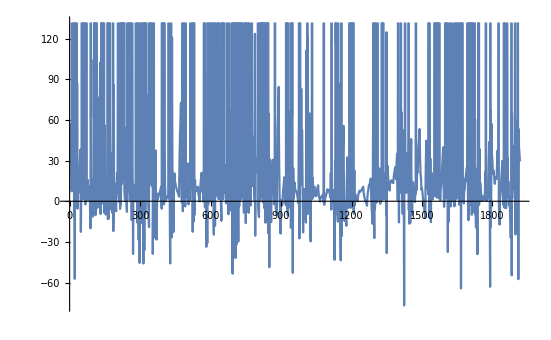

```mathematica
ListLinePlot[InverseWaveletTransform[thr]]
```

## 按字蚁群算法

```mathematica
data=Import["D:\\cdata.csv",CharacterEncoding->"UTF-8"];
data=data[[2;;-1]];
```

```mathematica
data//Length
```

38000

```mathematica
characters=Union[Flatten[Characters[#]&/@data]];
```

```mathematica
characters//Length
```

1917

```mathematica
ClearAll[cPosition];
cPosition[c_]:=0
(cPosition[characters[[#]]]=#)&/@Range[Length[characters]];
```

```mathematica
ClearAll[ToSequence];
ToSequence[x_]:=Module[{c=Characters[x]},
(cPosition[#])&/@c[[1]]
]
```

```mathematica
s=SparseArray[{},{1,1}Length[characters],1/Length[characters]];
n=Floor[Length[data]/1000];
batchSize=Floor[Length[data]/n];
remainder=Length[data]-batchSize×n;
Dynamic[ProgressIndicator[see/n]]
(see=#;
start=1+batchSize (#-1);end=batchSize #;((s[[#[[1]],#[[2]]]]=Min[s[[#[[1]],#[[2]]]]+1/batchSize,1])&/@Partition[ToSequence[#],2,1])&/@data[[start;;end]];
s=1/Length[characters]+0.9(s-1/Length[characters]))&/@Range[n];
```

```mathematica
SortBy[({characters[[#]],s[[cPosition["的"],cPosition[characters[[#]]]]]})&/@Flatten[Position[s[[cPosition["的"],All]]//Normal,n_/;n≥0.3]],Last]
```

{{就,0.314169},{元,0.656279},{信,0.729141},{身,0.900052}}

```mathematica
With[{word="额度"},SortBy[({characters[[#]],s[[cPosition[word],cPosition[characters[[#]]]]]})&/@Flatten[Position[s[[cPosition[word],All]]//Normal,n_/;n≥0.1]],Last]]
```

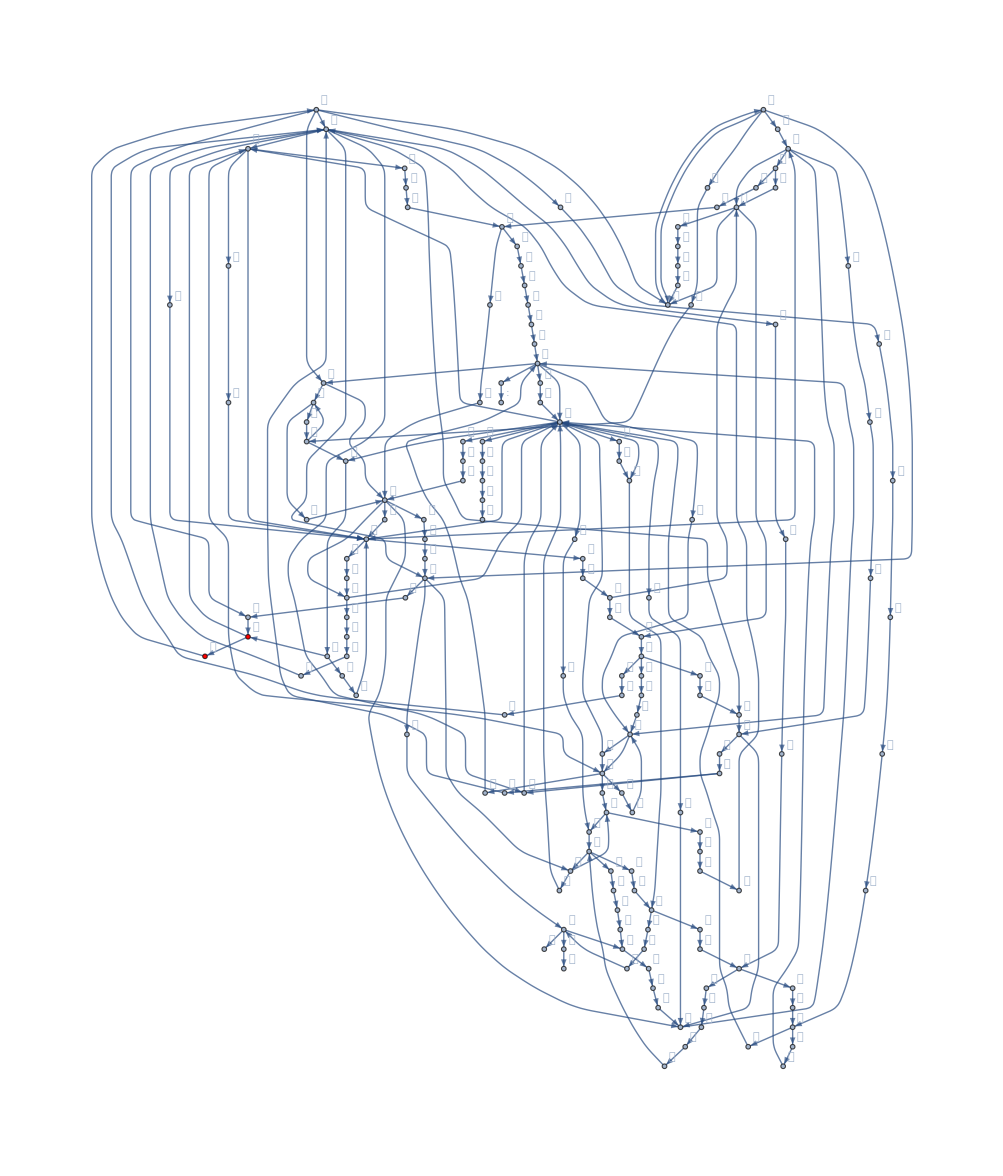

```mathematica
Graph[(characters[[#[[1]]]]->characters[[#[[2]]]])&/@Position[Normal@s,n_/;n≥0.3],VertexLabels->"Name",VertexStyle->{"爱"->Red,"又"->Red},GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
ToModel[lst__,threshold_]:=Module[{seq=ToSequence[lst],start="",end="",res={}},
start=If[s[[seq[[1]],seq[[2]]]]>threshold,characters[[seq[[1]]]],"_"];
end=If[s[[seq[[-2]],seq[[-1]]]]>threshold,characters[[seq[[-1]]]],"_"];
res=(If[s[[seq[[#-1]],seq[[#]]]]>threshold||s[[seq[[#]],seq[[#+1]]]]>threshold,characters[[seq[[#]]]],"_"])&/@Range[2,Length[seq]-1];
StringReplace[StringJoin[{start},res,{end}],"_"..->"_"]
]
```

```mathematica
model=GatherBy[({ToModel[#,0.3],#})&/@data,First];
```

```mathematica
Export["D:\\按字蚁群算法.xls",Sort@model]
```

D:\按字蚁群算法.xls

```mathematica
Print[#]&/@Sort[model[[All,1,1]]];
```

爱又米_您的_额元_

_验证码_有效_分钟_

爱又米_官方_您的_额元_

爱又米爱又米_您的_额元_

爱又米审核通过_额度_取现_

爱又米_爱又米您的_及时_您的_官方客服热线

爱又米_提醒_还款_如有问题请拨打官方客服电话

爱又米亲爱的_审核已通过当前总额度元取现额度元

爱又米亲爱的_经评估当前审核未通过_爱又米_信用额度

爱又米审核通过_信用额度_额度_任何人_账户_ :_

爱又米您的身份信息审核未通过我们暂时无法向您提供服务

爱又米亲爱的_经评估您暂时无法申请信用额度请天后再尝试

爱又米亲爱的_您的元_征信系统_还款_您的信用如有_官方客服_

爱又米亲爱的_审核未通过经评估您暂时无法申请信用额度请天后再尝试

爱又米亲爱的元_您的元_征信系统_还款_您的信用如有_官方客服_

爱又米验证码分钟内有效请确保本人操作打死都不能告诉任何人哦！唯一热线

爱又米亲爱的_您申请的元_放款_征信系统_还款_您的信用如有_官方客服

爱又米亲爱的_您的_审核未通过经系统评估暂时无法申请信用额度请天后再尝试

爱又米_提醒_您的月信用账单已_总额_还款_征信系统_还款_您的信用如有_官方客服

爱又米亲爱的_您的月信用账单_还款_您的_还款行为_征信系统避免逾期_及时还款_还款请_

爱又米亲爱的_您的月信用账单已逾期_逾期费逾期行为_征信系统为避免您的_信用记录请尽快还款

爱又米亲爱的_您的_账单已_还款金额_及时还款_银行_征信系统_还款_您的信用如有_官方客服

爱又米亲爱的_您申请的元放款失败请更换银行卡重新提交非常抱歉给您造成了不便如有问题请拨打官方客服电话

爱又米亲爱的_您的还款_还款金额_您的_还款行为_征信系统避免逾期_及时还款_银行_还款请_如有_官方客服

爱又米您的信用账户因购买商品发生扣款金额元若非本人交易请立即拨打官方客服热线反馈还款请下载爱又米进行还款 :

爱又米还款_提醒_您的_账单_金额_还款_爱又米_接入央行征信_的信用行为_放款_服务如有问题请拨打官方客服电话

爱又米还款_提醒亲爱的_您的_还款_还款金额_爱又米_还款_进行扣款_还款请_还款进入链接下载点击信用钱包及时还款

爱又米亲爱的_您的_账单已逾期_逾期费逾期行为_征信系统为避免您的_信用记录请尽快还款_银行_如有问题请拨打官方客服电话

爱又米亲爱的元_您的_账单已逾期_逾期费逾期行为_征信系统为避免您的_信用记录请尽快还款_银行_如有问题请拨打官方客服电话

爱又米还款_提醒亲爱的_您的月信用账单_还款_逾期还款_逾期费_影响您_央行_征信记录_及时还款_还款请_进入链接下载点击信用钱包及时还款

爱又米还款_提醒亲爱的_响您的月信用账单_还款_逾期还款_逾期费_影响您_央行_征信记录_及时还款_还款请_进入链接下载点击信用钱包及时还款

爱又米逾期提醒亲爱的_您月_账单已逾期逾期费用已开始计算逾期记录接入央行征信系统为避免影响您的就业和购房等行为请尽快还款进入链接下载点击信用钱包及时还款

爱又米逾期提醒亲爱的_您月信用账单已逾期逾期费用已开始计算逾期记录接入央行征信系统为避免影响您的就业和购房等行为请尽快还款进入链接下载点击信用钱包及时还款

## 模拟蚁群优化

```mathematica
data=Import["D:\\data.csv",CharacterEncoding->"UTF-8"];
data=data[[2;;-1]];
```

```mathematica
data//Length
```

38000

```mathematica
characters=Union[Flatten[StringSplit[#,","]&/@data]];
```

```mathematica
characters//Length
```

11492

```mathematica
ClearAll[cPosition];
cPosition[c_]:=0
(cPosition[characters[[#]]]=#)&/@Range[Length[characters]];
```

```mathematica
ClearAll[ToSequence];
ToSequence[x_]:=Module[{c=StringSplit[x,","]},
(cPosition[#])&/@c[[1]]
]
```

```mathematica
s=SparseArray[{},{1,1}Length[characters],1/Length[characters]];
n=Floor[Length[data]/1000];
batchSize=Floor[Length[data]/n];
remainder=Length[data]-batchSize×n;
Dynamic[ProgressIndicator[see/n]]
(see=#;
start=1+batchSize (#-1);end=batchSize #;((s[[#[[1]],#[[2]]]]=Min[s[[#[[1]],#[[2]]]]+1/batchSize,1])&/@Partition[ToSequence[#],2,1])&/@data[[start;;end]];
s=1/Length[characters]+0.9(s-1/Length[characters]))&/@Range[n];
```

```mathematica
Dynamic[ProgressIndicator[see/Length[data]]]
(see=#;(s[[#[[1]],#[[2]]]]=(2+s[[#[[1]],#[[2]]]])/4)&/@Partition[ToSequence[data[[#]]],2,1];
s=1/Length[characters]+0.8(s-1/Length[characters]))&/@Range[Length[data]];
```

```mathematica
SortBy[({characters[[#]],s[[cPosition["的"],cPosition[characters[[#]]]]]})&/@Flatten[Position[s[[cPosition["的"],All]]//Normal,n_/;n≥0.1]],Last]
```

{{借,0.109496},{余额,0.109496},{服务,0.109496},{额外,0.109496},{自助,0.134245},{嗨,0.160229},{月,0.166844},{个人,0.166844},{就业,0.31387},{元,0.65613},{信用,0.729024},{身份,0.900009}}

```mathematica
With[{word="额度"},SortBy[({characters[[#]],s[[cPosition[word],cPosition[characters[[#]]]]]})&/@Flatten[Position[s[[cPosition[word],All]]//Normal,n_/;n≥0.1]],Last]]
```

{{呢,0.166844},{请,0.387474},{元,0.478342}}

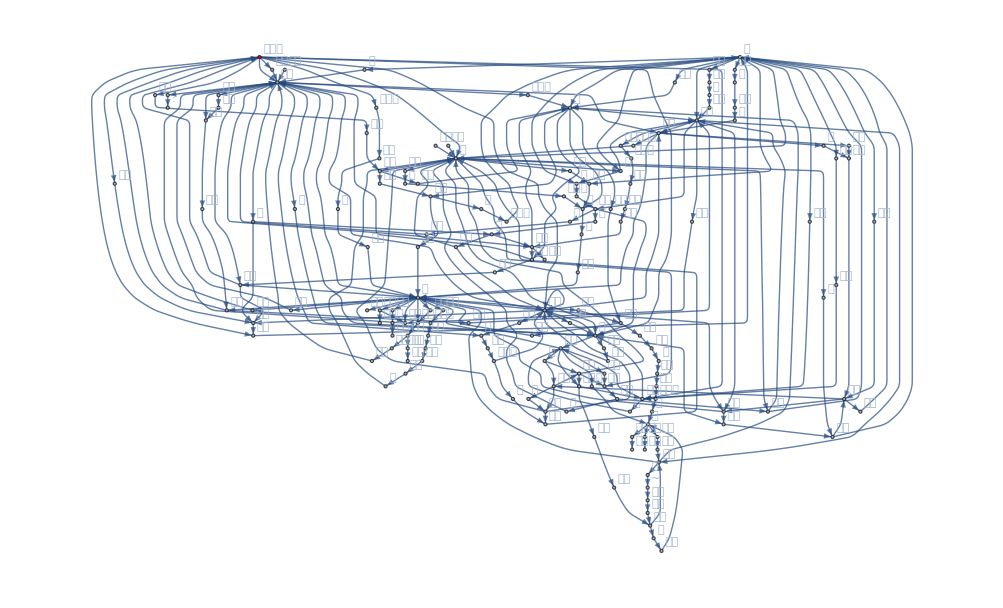

```mathematica
Graph[(characters[[#[[1]]]]->characters[[#[[2]]]])&/@Position[Normal@s,n_/;n≥0.1],VertexLabels->"Name",VertexStyle->{"爱又米"->Red},GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
ToModel[lst__,threshold_]:=Module[{seq=ToSequence[lst],start="",end="",res={}},
start=characters[[seq[[1]]]];
end=characters[[seq[[-1]]]];
res=(If[s[[seq[[#-1]],seq[[#]]]]>threshold||s[[seq[[#]],seq[[#+1]]]]>threshold,characters[[seq[[#]]]],"_"])&/@Range[2,Length[seq]-1];
StringReplace[StringJoin[{start},res,{end}],"_"..->"_"]
]
```

```mathematica
model=GatherBy[({ToModel[#,0.1],#})&/@data,First];
```

```mathematica
Export["D:\\分词蚁群算法.xls",model]
```

D:\分词蚁群算法.xls

```mathematica
model[[All,1,1]]//Length
```

31

```mathematica
s[[cPosition["账单"],cPosition["已出"]]]
```

0.0744217

```mathematica
s[[cPosition["已出"],cPosition["本期"]]]
```

0.0744217

```mathematica
s[[cPosition["本期"],cPosition["应"]]]
```

0.0471842

```mathematica
Grid[{ToModel[#,0.0317756],#}&/@data[[1;;100]],Frame->True]
```

## 频率

```mathematica
data=Import["D:\\data.csv",CharacterEncoding->"UTF-8"];
data=data[[2;;-1]];
```

```mathematica
data//Length
```

38000

```mathematica
characters=Union[Flatten[StringSplit[#,","]&/@data]];
```

```mathematica
characters//Length
```

11492

```mathematica
ClearAll[cPosition];
cPosition[c_]:=0
(cPosition[characters[[#]]]=#)&/@Range[Length[characters]];
```

```mathematica
ClearAll[ToSequence];
ToSequence[x_]:=Module[{c=StringSplit[x,","]},
(cPosition[#])&/@c[[1]]
]
```

```mathematica
ttl=Total[SparseArray[Flatten[(ind=#;({ind,cPosition[characters[[#]]]}->1)&/@ToSequence[data[[#]]])&/@Range[Length[data]]]]];
ToModel2[x_,threshold_]:=Module[{cc=StringSplit[x,","],res={}},
res=(If[ttl[[cPosition[#]]]≥threshold,#,"_"])&/@cc[[1]];
StringReplace[StringJoin[res],"_"..->"_"]
]
```

```mathematica
model=GatherBy[({ToModel2[#,4000],#})&/@data,First];
Export["D:\\词频阈值结果.xls",model]
```

D:\词频阈值结果.xls

```mathematica
model[[All,1,1]]
```

{爱又米温馨提醒_您的月信用账单_应还总额_请_月_还款本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服,爱又米亲爱的_您的元_已成功_本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服_,爱又米亲爱的_您申请的元已放款成功_您_本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服,爱又米_您成功_爱又米您的_为_及时_您的_咨询官方客服热线,爱又米亲爱的_评估您暂时无法申请信用额度请_,爱又米亲爱的_审核未通过_评估您暂时无法申请信用额度请_,爱又米审核通过啦！您已获得元信用额度_！额度_账户_ : _,爱又米亲爱的_的_评估您暂时无法申请信用额度请_,爱又米亲爱的_月审核未通过_评估您暂时无法申请信用额度请_,爱又米亲爱的_将_评估您暂时无法申请信用额度请_,爱又米温馨提醒_将_您的月信用账单_应还总额_请_月_还款本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服,爱又米亲爱的_月您的元_已成功_本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服_,爱又米亲爱的_元_您的元_已成功_本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服_,爱又米亲爱的元_您的元_已成功_本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服_,爱又米温馨提醒_如您的月信用账单_应还总额_请_月_还款本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服,爱又米温馨提醒_为您的月信用账单_应还总额_请_月_还款本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服,爱又米温馨提醒_元您的月信用账单_应还总额_请_月_还款本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服,爱又米亲爱的_您的月_账单已逾期_将_逾期行为_记入征信系统为避免您的_信用记录请尽快还款_如有问题请拨打官方客服电话,爱又米亲爱的_您的月信用账单已逾期_将_逾期行为_记入征信系统为避免您的_信用记录请尽快还款,爱又米亲爱的_您的月信用账单_还款_还_您的借还款行为_记入征信系统避免逾期请及时还款_已还款请_,爱又米亲爱的_您的_账单_还款金额_请及时还款_本次_将记入征信系统保持良好借还款有利于提升您的信用如有疑问请咨询官方客服,爱又米亲爱的_您的还款_还款金额_您的借还款行为_记入征信系统避免逾期请及时还款_已还款请_如有疑问请咨询官方客服,爱又米爱又米_您的_元已经_成功请_,爱又米_您的_元已经_成功请_,爱又米还款成功提醒_您的_账单应还金额已经还款成功爱又米已接入央行征信_的信用行为_您获得_放款_的服务如有问题请拨打官方客服电话,爱又米_官方_您的_元已经_成功请_,爱又米亲爱的_有_您的还款_还款金额_您的借还款行为_记入征信系统避免逾期请及时还款_已还款请_如有疑问请咨询官方客服,爱又米亲爱的_月您的月信用账单已逾期_将_逾期行为_记入征信系统为避免您的_信用记录请尽快还款,爱又米还款成功提醒_月_您的_账单应还金额已经还款成功爱又米已接入央行征信_的信用行为_您获得_放款_的服务如有问题请拨打官方客服电话,爱又米亲爱的应_您的月信用账单已逾期_将_逾期行为_记入征信系统为避免您的_信用记录请尽快还款,爱又米审核通过啦！_额度_取现_！_,爱又米还款_提醒亲爱的_您的月信用账单_还款_还_逾期还款将_您_央行的_征信记录请_及时还款_已还款_进入链接下载点击信用钱包及时还款,爱又米还款_提醒亲爱的_您的_还款_还款金额_爱又米将_还款_已还款_还款进入链接下载点击信用钱包及时还款,爱又米还款_提醒亲爱的_应您的月信用账单_还款_还_逾期还款将_您_央行的_征信记录请_及时还款_已还款_进入链接下载点击信用钱包及时还款,爱又米还款_提醒亲爱的_月您的月信用账单_还款_还_逾期还款将_您_央行的_征信记录请_及时还款_已还款_进入链接下载点击信用钱包及时还款,爱又米还款_提醒亲爱的有_您的月信用账单_还款_还_逾期还款将_您_央行的_征信记录请_及时还款_已还款_进入链接下载点击信用钱包及时还款,爱又米还款_提醒亲爱的_元您的月信用账单_还款_还_逾期还款将_您_央行的_征信记录请_及时还款_已还款_进入链接下载点击信用钱包及时还款,爱又米逾期提醒亲爱的_您月_账单已逾期逾期_已_逾期记录接入央行征信系统为避免_您的_行为请尽快还款进入链接下载点击信用钱包及时还款,爱又米逾期提醒亲爱的_您月信用账单已逾期逾期_已_逾期记录接入央行征信系统为避免_您的_行为请尽快还款进入链接下载点击信用钱包及时还款,爱又米逾期提醒亲爱的_元您月信用账单已逾期逾期_已_逾期记录接入央行征信系统为避免_您的_行为请尽快还款进入链接下载点击信用钱包及时还款,爱又米亲爱的_您的_审核未通过_系统评估暂时无法申请信用额度请_,爱又米亲爱的_评估_审核未通过请_爱又米_获得_元信用额度,爱又米温馨提醒_您已还款_元如有问题请拨打官方客服电话,爱又米温馨提醒_元您已还款_元如有问题请拨打官方客服电话,爱又米温馨提醒_成功您已还款_元如有问题请拨打官方客服电话,爱又米亲爱的_有_评估_审核未通过请_爱又米_获得_元信用额度,爱又米亲爱的_您申请的元放款_请_您_如有问题请拨打官方客服电话,爱又米亲爱的_审核已通过_总额_取现额度元,爱又米亲爱的_月_审核已通过_总额_取现额度元,爱又米_请_！_,_为_请_成功_！,爱又米亲爱的_月审核已通过_总额_取现额度元,爱又米亲爱的的_审核已通过_总额_取现额度元,爱又米您的信用账户_金额元_请_拨打官方客服热线_还款请下载爱又米_还款 :,爱又米您的_审核未通过_暂时无法_您_服务}

```mathematica
premodel=model[[All,1,1]];
premodelCount=Length[premodel];
s=SparseArray[{},{1,1}premodelCount];
(now=#;(s[[now,#]]=EditDistance[premodel[[now]],premodel[[#]]])&/@Range[#+1,premodelCount])&/@Range[premodelCount];
```

```mathematica
Needs["HierarchicalClustering`"]
```

Agglomerate::ties: 13 ties have been detected; reordering input may produce a different result.

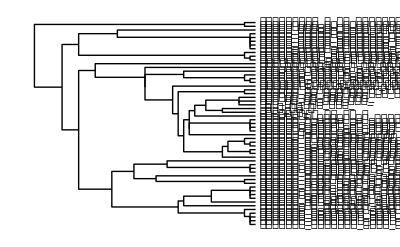

```mathematica
DendrogramPlot[premodel,LeafLabels->premodel,Orientation->Left]
```

```mathematica
DistanceMatrix[premodel]
```

{{0,20,20,49,56,55,57,55,54,55,2,21,21,20,1,1,1,41,40,40,14,35,55,55,46,55,36,41,48,40,57,47,50,48,48,48,48,54,52,53,51,54,47,48,48,54,50,56,56,57,59,56,56,50,55},{20,0,8,38,42,41,47,40,41,41,22,1,2,1,21,21,21,34,38,40,14,31,43,43,47,43,33,39,49,39,46,53,45,54,54,54,54,50,51,52,36,42,40,40,39,42,36,43,43,47,48,43,44,44,44},{20,8,0,43,46,46,52,45,46,46,22,9,9,9,21,21,21,36,38,43,13,31,47,47,48,47,32,39,50,39,52,54,47,55,55,55,55,50,51,52,42,46,45,45,44,46,35,47,47,50,52,47,48,48,49},{49,38,43,0,24,25,26,24,26,24,51,39,40,39,50,50,50,43,35,39,46,39,20,22,47,21,41,36,49,36,24,54,42,55,55,55,55,55,56,57,26,25,20,20,20,26,22,23,22,24,25,23,23,31,20},{56,42,46,24,0,6,23,2,7,2,57,43,43,43,57,57,57,48,36,38,50,46,15,15,57,15,48,37,59,37,18,57,44,58,58,58,58,56,57,58,12,17,22,23,23,19,23,13,15,16,20,14,14,32,16},{55,41,46,25,6,0,25,5,1,5,57,42,43,42,56,56,56,47,35,37,49,46,20,20,57,20,47,36,59,36,20,56,43,57,57,57,57,55,56,57,6,15,24,24,25,17,22,14,16,22,25,15,15,31,13},{57,47,52,26,23,25,0,24,26,24,58,48,48,48,57,57,57,52,40,42,55,50,23,23,55,23,51,41,57,41,15,59,45,60,60,60,60,59,60,60,28,25,25,25,26,25,28,23,24,24,27,23,23,32,24},{55,40,45,24,2,5,24,0,6,1,57,41,42,41,56,56,56,46,34,36,48,44,16,17,56,17,46,35,58,35,20,55,42,56,56,56,56,55,56,57,10,19,22,23,24,18,21,15,14,18,21,15,14,31,16},{54,41,46,26,7,1,26,6,0,6,56,41,43,42,55,55,55,46,34,36,50,46,21,21,57,21,47,35,59,35,21,55,43,56,56,56,56,54,55,56,6,15,25,25,25,17,22,15,15,23,26,14,16,32,14},{55,41,46,24,2,5,24,1,6,0,56,42,43,42,56,56,56,46,34,37,49,45,16,17,57,17,47,35,59,35,20,56,42,57,57,57,57,55,56,57,11,19,22,23,24,18,22,15,14,18,21,15,15,31,16},{2,22,22,51,57,57,58,57,56,56,0,22,21,22,2,2,2,43,42,42,16,37,57,57,48,57,36,42,47,42,59,47,51,48,48,48,48,54,52,53,53,56,49,49,49,55,52,58,57,59,61,58,58,52,57},{21,1,9,39,43,42,48,41,41,42,22,0,2,2,21,21,21,35,39,41,15,32,44,44,48,44,33,38,48,40,47,54,46,54,53,55,54,51,51,52,37,43,41,41,40,43,37,44,43,48,49,43,45,45,45},{21,2,9,40,43,43,48,42,43,43,21,2,0,1,22,22,21,36,40,42,15,33,44,44,47,45,32,40,48,40,48,55,47,55,55,55,54,51,52,52,38,44,41,41,41,43,37,45,44,49,49,45,45,46,46},{20,1,9,39,43,42,48,41,42,42,22,2,1,0,21,21,21,35,39,41,15,32,43,44,47,44,33,40,49,39,47,54,46,55,55,54,55,51,52,53,37,43,40,40,40,43,37,44,44,48,49,44,44,45,45},{1,21,21,50,57,56,57,56,55,56,2,21,22,21,0,1,1,42,41,41,15,36,56,56,47,56,37,41,48,41,58,48,51,48,48,49,48,55,53,53,52,55,48,48,49,55,51,57,57,58,60,57,57,51,56},{1,21,21,50,57,56,57,56,55,56,2,21,22,21,1,0,1,42,41,41,15,36,56,56,47,56,37,41,48,41,58,48,51,48,48,49,48,55,53,53,52,55,48,48,49,55,51,57,57,58,59,57,57,51,56},{1,21,21,50,57,56,57,56,55,56,2,21,21,21,1,1,0,42,41,41,15,36,56,56,47,56,37,41,48,41,58,48,51,48,48,49,47,55,53,52,52,55,48,47,49,55,51,57,57,58,60,57,57,51,56},{41,34,36,43,48,47,52,46,46,46,43,35,36,35,42,42,42,0,16,33,37,30,48,48,40,48,32,17,42,17,52,48,51,49,49,49,49,35,37,38,44,47,39,39,39,47,34,49,47,53,54,48,48,48,48},{40,38,38,35,36,35,40,34,34,34,42,39,40,39,41,41,41,16,0,22,40,36,37,37,53,37,38,1,55,1,40,43,38,44,44,44,44,37,35,36,32,35,40,41,41,35,35,36,35,40,42,35,36,36,37},{40,40,43,39,38,37,42,36,36,37,42,41,42,41,41,41,41,33,22,0,38,18,38,39,52,38,20,23,54,23,42,38,40,39,39,39,39,47,45,46,34,39,40,40,40,38,35,40,38,42,44,39,39,36,40},{14,14,13,46,50,49,55,48,50,49,16,15,15,15,15,15,15,37,40,38,0,26,52,52,44,52,28,41,46,41,54,48,45,49,49,49,49,52,54,55,45,48,49,49,49,47,43,51,51,54,56,52,51,49,51},{35,31,31,39,46,46,50,44,46,45,37,32,33,32,36,36,36,30,36,18,26,0,46,47,47,46,2,37,49,37,49,45,43,46,46,46,46,49,50,51,41,46,44,44,44,45,38,48,47,50,51,48,47,45,47},{55,43,47,20,15,20,23,16,21,16,57,44,44,43,56,56,56,48,37,38,52,46,0,3,53,3,48,38,55,37,13,58,44,59,59,58,59,57,59,59,22,22,20,21,22,23,23,16,17,12,13,17,16,30,16},{55,43,47,22,15,20,23,17,21,17,57,44,44,44,56,56,56,48,37,39,52,47,3,0,53,3,49,38,55,38,13,58,44,59,59,59,59,57,59,59,22,22,20,20,22,23,23,14,16,9,10,15,15,29,14},{46,47,48,47,57,57,55,56,57,57,48,48,47,47,47,47,47,40,53,52,44,47,53,53,0,53,47,54,2,53,57,50,47,51,51,51,51,53,54,55,55,53,41,42,41,53,42,57,57,59,60,57,57,55,53},{55,43,47,21,15,20,23,17,21,17,57,44,45,44,56,56,56,48,37,38,52,46,3,3,53,0,48,38,55,38,13,57,43,58,58,58,58,57,59,59,22,22,20,21,22,24,23,16,17,12,13,17,17,30,15},{36,33,32,41,48,47,51,46,47,47,36,33,32,33,37,37,37,32,38,20,28,2,48,49,47,48,0,38,48,38,51,47,45,47,47,46,47,51,51,52,43,48,46,46,46,46,40,49,49,52,53,49,49,47,49},{41,39,39,36,37,36,41,35,35,35,42,38,40,40,41,41,41,17,1,23,41,37,38,38,54,38,38,0,54,2,41,44,39,44,43,45,44,38,36,36,33,36,41,41,42,36,36,37,36,41,43,36,37,37,38},{48,49,50,49,59,59,57,58,59,59,47,48,48,49,48,48,48,42,55,54,46,49,55,55,2,55,48,54,0,55,59,50,48,51,51,51,51,53,55,56,57,55,43,43,43,54,44,59,58,61,61,59,59,57,55},{40,39,39,36,37,36,41,35,35,35,42,40,40,39,41,41,41,17,1,23,41,37,37,38,53,38,38,2,55,0,41,44,39,45,45,44,45,38,36,37,33,36,40,41,41,36,36,37,36,41,43,36,37,37,38},{57,46,52,24,18,20,15,20,21,20,59,47,48,47,58,58,58,52,40,42,54,49,13,13,57,13,51,41,59,41,0,61,45,62,62,62,62,59,60,61,24,20,23,24,25,22,27,12,14,11,14,13,13,30,13},{47,53,54,54,57,56,59,55,55,56,47,54,55,54,48,48,48,48,43,38,48,45,58,58,50,57,47,44,50,44,61,0,25,1,1,1,1,34,32,33,54,54,57,57,57,53,54,59,57,61,63,58,58,52,58},{50,45,47,42,44,43,45,42,43,42,51,46,47,46,51,51,51,51,38,40,45,43,44,44,47,43,45,39,48,39,45,25,0,26,26,26,26,35,37,38,40,37,42,43,43,38,41,43,43,47,49,44,43,41,44},{48,54,55,55,58,57,60,56,56,57,48,54,55,55,48,48,48,49,44,39,49,46,59,59,51,58,47,44,51,45,62,1,26,0,1,2,1,35,33,33,55,55,58,58,58,54,55,60,58,62,64,59,59,53,59},{48,54,55,55,58,57,60,56,56,57,48,53,55,55,48,48,48,49,44,39,49,46,59,59,51,58,47,43,51,45,62,1,26,1,0,2,1,35,33,33,55,55,58,58,58,54,55,60,58,62,64,59,59,53,59},{48,54,55,55,58,57,60,56,56,57,48,55,55,54,49,49,49,49,44,39,49,46,58,59,51,58,46,45,51,44,62,1,26,2,2,0,2,35,33,34,55,55,58,58,58,54,55,60,58,62,64,59,59,53,59},{48,54,55,55,58,57,60,56,56,57,48,54,54,55,48,48,47,49,44,39,49,46,59,59,51,58,47,44,51,45,62,1,26,1,1,2,0,35,33,32,55,55,58,57,58,54,55,60,58,62,64,59,59,53,59},{54,50,50,55,56,55,59,55,54,55,54,51,51,51,55,55,55,35,37,47,52,49,57,57,53,57,51,38,53,38,59,34,35,35,35,35,35,0,2,3,51,53,56,57,57,53,54,56,54,60,62,55,56,54,57},{52,51,51,56,57,56,60,56,55,56,52,51,52,52,53,53,53,37,35,45,54,50,59,59,54,59,51,36,55,36,60,32,37,33,33,33,33,2,0,1,53,55,57,58,58,55,55,57,56,61,63,56,58,53,58},{53,52,52,57,58,57,60,57,56,57,53,52,52,53,53,53,52,38,36,46,55,51,59,59,55,59,52,36,56,37,61,33,38,33,33,34,32,3,1,0,54,56,58,57,59,56,56,58,57,62,64,57,59,54,59},{51,36,42,26,12,6,28,10,6,11,53,37,38,37,52,52,52,44,32,34,45,41,22,22,55,22,43,33,57,33,24,54,40,55,55,55,55,51,53,54,0,15,27,27,28,17,24,18,17,26,29,18,17,31,16},{54,42,46,25,17,15,25,19,15,19,56,43,44,43,55,55,55,47,35,39,48,46,22,22,53,22,48,36,55,36,20,54,37,55,55,55,55,53,55,56,15,0,25,26,26,2,23,15,14,22,24,15,15,32,17},{47,40,45,20,22,24,25,22,25,22,49,41,41,40,48,48,48,39,40,40,49,44,20,20,41,20,46,41,43,40,23,57,42,58,58,58,58,56,57,58,27,25,0,1,2,26,13,22,22,22,24,23,22,31,22},{48,40,45,20,23,24,25,23,25,23,49,41,41,40,48,48,47,39,41,40,49,44,21,20,42,21,46,41,43,41,24,57,43,58,58,58,57,57,58,57,27,26,1,0,2,27,14,22,23,23,25,23,22,32,22},{48,39,44,20,23,25,26,24,25,24,49,40,41,40,49,49,49,39,41,40,49,44,22,22,41,22,46,42,43,41,25,57,43,58,58,58,58,57,58,59,28,26,2,2,0,27,14,23,24,24,25,23,23,33,23},{54,42,46,26,19,17,25,18,17,18,55,43,43,43,55,55,55,47,35,38,47,45,23,23,53,24,46,36,54,36,22,53,38,54,54,54,54,53,55,56,17,2,26,27,27,0,24,17,16,24,26,17,17,32,19},{50,36,35,22,23,22,28,21,22,22,52,37,37,37,51,51,51,34,35,35,43,38,23,23,42,23,40,36,44,36,27,54,41,55,55,55,55,54,55,56,24,23,13,14,14,24,0,23,23,25,28,23,24,31,24},{56,43,47,23,13,14,23,15,15,15,58,44,45,44,57,57,57,49,36,40,51,48,16,14,57,16,49,37,59,37,12,59,43,60,60,60,60,56,57,58,18,15,22,22,23,17,23,0,2,15,18,1,1,32,12},{56,43,47,22,15,16,24,14,15,14,57,43,44,44,57,57,57,47,35,38,51,47,17,16,57,17,49,36,58,36,14,57,43,58,58,58,58,54,56,57,17,14,22,23,24,16,23,2,0,17,19,1,2,32,14},{57,47,50,24,16,22,24,18,23,18,59,48,49,48,58,58,58,53,40,42,54,50,12,9,59,12,52,41,61,41,11,61,47,62,62,62,62,60,61,62,26,22,22,23,24,24,25,15,17,0,6,16,16,31,15},{59,48,52,25,20,25,27,21,26,21,61,49,49,49,60,59,60,54,42,44,56,51,13,10,60,13,53,43,61,43,14,63,49,64,64,64,64,62,63,64,29,24,24,25,25,26,28,18,19,6,0,19,19,33,18},{56,43,47,23,14,15,23,15,14,15,58,43,45,44,57,57,57,48,35,39,52,48,17,15,57,17,49,36,59,36,13,58,44,59,59,59,59,55,56,57,18,15,23,23,23,17,23,1,1,16,19,0,2,33,13},{56,44,48,23,14,15,23,14,16,15,58,45,45,44,57,57,57,48,36,39,51,47,16,15,57,17,49,37,59,37,13,58,43,59,59,59,59,56,58,59,17,15,22,22,23,17,24,1,2,16,19,2,0,32,13},{50,44,48,31,32,31,32,31,32,31,52,45,46,45,51,51,51,48,36,36,49,45,30,29,55,30,47,37,57,37,30,52,41,53,53,53,53,54,53,54,31,32,31,32,33,32,31,32,32,31,33,33,32,0,29},{55,44,49,20,16,13,24,16,14,16,57,45,46,45,56,56,56,48,37,40,51,47,16,14,53,15,49,38,55,38,13,58,44,59,59,59,59,57,58,59,16,17,22,22,23,19,24,12,14,15,18,13,13,29,0}}

```mathematica
s[[1]]//Normal
```

{0,20,20,49,56,55,57,55,54,55,2,21,21,20,1,1,1,41,40,40,14,35,55,55,46,55,36,41,48,40,57,47,50,48,48,48,48,54,52,53,51,54,47,48,48,54,50,56,56,57,59,56,56,50,55}

```mathematica
ttl
```

{12,2000,4000,4000,14,30,8,4,2000,2,18,3,4,4,6012,34,2,4,5,4,4,2,8,2,2,4,2004,2,8,2000,2064,6,1,2,2,8,2,12,2,2,8,2,9,8,2,2002,2,6,4,4,2,2,2,2002,4,26,2,10,2,2002,1,4,2,10,6,6,2,2,2,2,6000,2,4,8,2,4,2,6,4,14615,2,2,9,4,4,2,12,10,2,1990,14,3392,22,2,2,10,3,2,5,1,4,2,21,2,2,4,6,2,132,14,10,2,12,8,4,2,2,6,4,2,2,2000,22,10,4,2,6,1,17,2,11232,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,104}
 |  |  |  |